# HW 3: Astro 735

## Elijah Bernstein-Cooper

#### 1a

```mathematica
a'[a_]:=H0 * a*(Ωm0 * a0^3/a^3+ Ωk0*a0^2/a^2+ΩΛ0)^(1/2);
a''[a_] :=D[a'[a],a];
Simplify[D[a'[a],a]]
mina:=Solve[a''[a] ==0,a]
```

(-a0^3 H0 Ωm0+2 a^3 H0 ΩΛ0)/(2 a^3 √((a0^2 Ωk0)/a^2+(a0^3 Ωm0)/a^3+ΩΛ0))

#### 1b

```mathematica
mina[[2]]
amin'[a_]:=H0 * amin*(Ωm0 * a0^3/a^3+ Ωk0*a0^2/a^2+ΩΛ0)^(1/2);
Simplify[amin'[a]^2/.mina[[2]]]
```

{a→(a0 Ωm0^(1/3))/(2^(1/3) ΩΛ0^(1/3))}

amin^2 H0^2 ((2^(2/3) Ωk0 ΩΛ0^(2/3))/Ωm0^(2/3)+3 ΩΛ0)

#### 1c

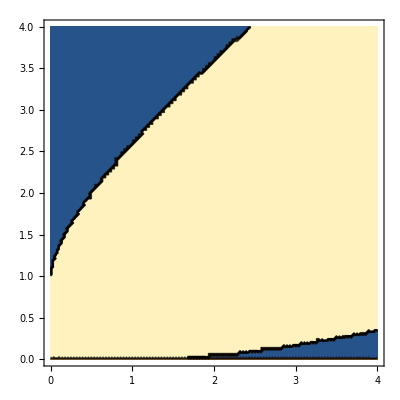

```mathematica
ContourPlot[Sign[3*ΩΛ0+Ωk0*((2*ΩΛ0)/Ωm0)^(2/3)/.{Ωk0->1-(ΩΛ0+Ωm0)}],{Ωm0,0,4},{ΩΛ0,0,4}]
```

The plot above shows the sign of the argument 3ΩΛ0+Ωk((2ΩΛ0)/Ωm0)^(2/3) where the y axis is ΩΛ0 and the x axis is Ωm0, blue is negative and yellow is positive. When this argument is negative, the universe is closed. For parameter values in the top-left corner, the space of the universe will have started as in the Big Bang, starting from a point source, expanding to a maximum, then contracting back to a point source. For parameter values in the bottom-right corner, the space of the universe will start as infinite, contract to a minimum, and expand to back to infinity.

#### 2a

```mathematica
(*h :=6.62*10^(10;)
c :=3*10^10;
k:=1.38*10^16;*)
B[T_,ν_]:=(2*h*ν^3/c^2)/(Exp[h*ν/(k*T)]-1);
Simplify[D[B[T,ν], ν]]
NSolve[ (-3 (-1+ⅇ^((h ν)/(k T))) k T+ⅇ^((h ν)/(k T)) h ν)==0,ν]
νmax0:=NSolve[D[B[T,ν], ν]==0,ν]
νmax0[[1]]
(*where for z > -1/e, the ProductLog is a positive constant*)
```

-(2 h ν^2 (-3 (-1+ⅇ^((h ν)/(k T))) k T+ⅇ^((h ν)/(k T)) h ν))/(c^2 (-1+ⅇ^((h ν)/(k T)))^2 k T)

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{ν→0.},{ν→(2.82144 k T)/h}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{ν→(2.82144 k T)/h}

#### 2b

```mathematica
ν0:=ν/.νmax0[[1]]/.{T->2.72548,h->6.62*10^10,k->1.38*10^16};
doppler[Δv_,ν0_]:=ν0*(1 + Δv/c)/.{c->3*10^10};
ν0(*Frequency of rest CMB*)
νp:=doppler[300*10^5,ν0] (*Frequency of CMB as measured with Sun's velocity*)
ν[T_]:=ν/.νmax[[1]]
NSolve[ν[T]==νp,T]/.{h->6.62*10^10,k->1.38*10^16}
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

1.603×10^6

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{T→2.72821}}

## 3a

```mathematica
dt[a_]:=H0*a(Ωm0/a^3+ΩΛ0)^(1/2);
t:=Integrate[1/dt[a],a];
t:=2/3*1/(H0*√ΩΛ0)Log[√(ΩΛ0/Ωm0 a^3)+√(1+ΩΛ0/Ωm0 a^3)]
tanθ:=(Ωm0/ΩΛ0)^(1/2)(1+z)^(3/2)
T[z_]=Simplify[t/.{a->1/(1+z)},tanθ]
Simplify[Sqrt[ΩΛ0/(1-ΩΛ0)]+Sqrt[ΩΛ0/(1-ΩΛ0)+1]]
```

(2 Log[√(ΩΛ0/((1+z)^3 Ωm0))+√(1+ΩΛ0/((1+z)^3 Ωm0))])/(3 H0 √ΩΛ0)

√(1/(1-ΩΛ0))+√(-ΩΛ0/(-1+ΩΛ0))